```mathematica
dampingdata = {{"ï»¿\"Latest: Time (s)\"","Latest: Position (m)","Latest: Velocity 1 (m/s)","Latest: Acceleration 1 (m/sÂ.b2)","Latest: Angle (rad)","Latest: Velocity 2 (rad/s)","Latest: Acceleration 2 (rad/sÂ.b2)"},{0.0666,0.6184976,-0.0123603603604,0.116128028819,0,0,0},{0.0999,0.6179488,-0.0078968968969,0.0909434069817,0,0,0},{0.1332,0.6179488,-0.00521881881882,0.0572238905572,0,0,0},{0.1665,0.6176744,-0.00434901568235,0.0325929867138,0,0,0},{0.1998,0.6176744,-0.00389122455789,0.0324402369225,0,0,0},{0.2331,0.6174,-0.00297564230898,0.0553336118902,0,0,0},{0.2664,0.6174,0,0.0721742763785,0,0,0},{0.2997,0.6174,0.00297564230898,0.0574721089681,0,0,0},{0.333,0.6176744,0.00412012012012,0.0286405858645,0,0,0},{0.3663,0.6176744,0.00457791124458,0.00305499582554,0,0,0},{0.3996,0.6179488,0.00526459793126,-0.0400968202103,0,0,0},{0.4329,0.6182232,0.00114447781114,-0.0582358579244,0,0,0},{0.4662,0.6179488,-0.00114447781114,-0.00973779919392,0,0,0},{0.4995,0.6179488,0.0016022689356,0.0173752887578,0,0,0},{0.5328,0.6182232,0.000915582248916,0.0215759080179,0,0,0},{0.5661,0.6179488,0.00183116449783,0.0500255566433,0,0,0},{0.5994,0.6182232,0.00549349349349,0.0504074311215,0,0,0},{0.6327,0.6184976,0.00503570236904,0.0589996068808,0,0,0},{0.666,0.6184976,0.00732465799132,0.0893586278972,0,0,0},{0.6993,0.618772,0.013962629296,-0.0414333808839,0,0,0},{0.7326,0.6193208,0.0187694361028,-0.665989089969,0,0,0},{0.7659,0.6209672,-0.0112158825492,-1.9193011274,0,0,0.0121446191213},{0.7992,0.620144,-0.0984250917584,-3.49281491479,0,0,0.0850123338493},{0.8325,0.6163024,-0.249496162829,-4.83033027466,0,0,0.425061669247},{0.8658,0.605052,-0.448406406406,-5.26967686182,0,0.0145589694027,1.15373881653},{0.8991,0.5855696,-0.627173840507,-4.8305212119,0,0.0582358776106,2.25889915657},{0.9324,0.5622456,-0.774124791458,-4.12252592933,0,0.203825571637,2.25889915657},{0.9657,0.533708,-0.902306306306,-3.31810734102,0.0174532925199,0.247502479845,1.15373881654},{0.999,0.5013288,-0.999358024691,-2.38996142177,0.0174532925199,0.262061449249,0.425061669253},{1.0323,0.4662056,-1.06253319987,-1.42515555262,0.0349065850399,0.262061449249,0.0850123338454},{1.0656,0.4297104,-1.09297630964,-0.486889959696,0.0349065850399,0.262061449248,0.012144619117},{1.0989,0.3926664,-1.09366299633,0.412615373688,0.0523598775598,0.262061449248,4.66352941508*^-12},{1.1322,0.3561712,-1.0659666333,1.3054379037,0.0523598775598,0.262061449249,5.91544757048*^-12},{1.1655,0.3207736,-1.005995996,2.1512898729,0.0698131700798,0.262061449249,-0.0121446191187},{1.1988,0.2883944,-0.917413413413,2.82300708004,0.0698131700798,0.262061449248,-0.0850123338354},{1.2321,0.259308,-0.813265932599,3.33662825321,0.0872664625997,0.262061449249,-0.425061669211},{1.2654,0.2337888,-0.69218018018,3.75229862272,0.0872664625997,0.247502479849,-1.1537388165},{1.2987,0.2132088,-0.565372038705,4.19202708436,0.10471975512,0.203825571641,-2.25889915659},{1.332,0.1953728,-0.414987654321,4.64015678452,0.10471975512,0.0582358776119,-2.25889915661},{1.3653,0.1849456,-0.246062729396,4.77362191465,0.10471975512,0.014558969403,-1.15373881655},{1.3986,0.1794576,-0.0883536870204,4.62220868405,0.10471975512,0,-0.425061669256},{1.4319,0.1791832,0.0640907574241,4.35642404723,0.10471975512,0,-0.0971569529729},{1.4652,0.1841224,0.20234367701,4.05798914252,0.10471975512,0,-0.0971569529729},{1.4985,0.1929032,0.332356356356,3.79545043876,0.10471975512,0,-0.412917050135},{1.5318,0.2063488,0.45595995996,3.47391212812,0.10471975512,-0.014558969403,-1.08087110182},{1.5651,0.2233616,0.571323323323,2.93031380841,0.10471975512,-0.0582358776119,-1.91884982121},{1.5984,0.2453136,0.657388054721,2.2108622915,0.10471975512,-0.189266602239,-1.51807739019},{1.6317,0.2680888,0.712780780781,1.62850371225,0.0872664625997,-0.203825571641,0.0242892382679},{1.665,0.2927848,0.761077744411,1.16987246394,0.0872664625997,-0.116471755223,-0.0850123338078},{1.6983,0.3191272,0.794267600934,0.625701332519,0.0872664625997,-0.203825571637,-0.449350907467},{1.7316,0.3462928,0.80617017017,-0.0202393473442,0.0698131700798,-0.203825571637,0.437206288371},{1.7649,0.3734584,0.794038705372,-0.713723399743,0.0698131700798,-0.116471755222,-8.55765658536*^-12},{1.7982,0.3998008,0.75787320654,-1.3825765483,0.0698131700798,-0.203825571638,-0.437206288374},{1.8315,0.4244968,0.700191524858,-1.98116479287,0.0523598775598,-0.203825571638,0.449350907496},{1.8648,0.4469976,0.6223670337,-2.460417263,0.0523598775598,-0.116471755222,0.0850123338598},{1.8981,0.4662056,0.532868868869,-2.82682582482,0.0523598775598,-0.203825571637,-0.0242892382365},{1.9314,0.4826696,0.434214881548,-3.16764879661,0.0349065850399,-0.189266602234,1.51807739017},{1.9647,0.4955664,0.321369369369,-3.46665651304,0.0349065850399,-0.0582358776106,1.91884982117},{1.998,0.5043472,0.198910243577,-3.62341598633,0.0349065850399,-0.0145589694027,1.0808711018},{2.0313,0.5087376,0.0766800133467,-3.64613751779,0.0349065850399,0,0.412917050125},{2.0646,0.5095608,-0.0471524858192,-3.53195704881,0.0349065850399,0,0.0971569529707},{2.0979,0.5054448,-0.164575909243,-3.21958372565,0.0349065850399,0,0.0971569529707},{2.1312,0.498036,-0.264374374374,-2.78882931424,0.0349065850399,0,0.412917050125},{2.1645,0.4876088,-0.351583583584,-2.30442153866,0.0349065850399,0.0145589694027,1.06872648268},{2.1978,0.4741632,-0.420938938939,-1.77896225666,0.0349065850399,0.0582358776106,1.84598210644},{2.2311,0.4585224,-0.46214014014,-1.47861797956,0.0349065850399,0.189266602234,1.19017267389},{2.2644,0.4437048,-0.507919252586,-1.4490227075,0.0523598775598,0.189266602234,-0.692243289914},{2.2977,0.4255944,-0.571552218886,-1.07287634648,0.0523598775598,0.0727948470133,-0.765111004638},{2.331,0.4041912,-0.594212879546,-0.295570846121,0.0523598775598,0.0727948470136,0.777255623776},{2.3643,0.3849832,-0.584141474808,0.328412051246,0.0523598775598,0.189266602236,0.777255623772},{2.3976,0.3652264,-0.564456456456,0.732817123652,0.0698131700798,0.189266602236,-0.777255623772},{2.4309,0.347116,-0.533555555556,1.04958200331,0.0698131700798,0.0727948470136,-0.777255623776},{2.4642,0.3295544,-0.49601668335,1.39097778682,0.0698131700798,0.0727948470133,0.765111004638},{2.4975,0.3136392,-0.442912912913,1.77953506838,0.0698131700798,0.189266602234,0.692243289914},{2.5308,0.2996448,-0.375617617618,2.1048921238,0.0872664625997,0.189266602234,-1.19017267389},{2.5641,0.2883944,-0.298937604271,2.29888435872,0.0872664625997,0.0582358776106,-1.84598210644},{2.5974,0.2796136,-0.218595261929,2.36093896143,0.0872664625997,0.0145589694027,-1.06872648268},{2.6307,0.2738512,-0.138252919586,2.3324893128,0.0872664625997,0,-0.412917050125},{2.664,0.2708328,-0.0672952952953,2.40600014986,0.0872664625997,0,-0.0850123338493},{2.6973,0.268912,0.0162515849183,2.6074389371,0.0872664625997,0,-0.0242892382427},{2.7306,0.2713816,0.113303303303,2.60171081993,0.0872664625997,0,-0.0850123338493},{2.7639,0.2768696,0.199139139139,2.30308497798,0.0872664625997,0,-0.412917050125},{2.7972,0.2851016,0.269638972306,1.87805868375,0.0872664625997,-0.0145589694027,-1.06872648268},{2.8305,0.2952544,0.323887220554,1.4402395945,0.0872664625997,-0.0582358776106,-1.83383748732},{2.8638,0.3070536,0.363715048382,1.05034575227,0.0872664625997,-0.189266602234,-1.10516034004},{2.8971,0.319676,0.393700367034,0.673053767815,0.0698131700798,-0.189266602234,1.09301572092},{2.9304,0.3336704,0.409494160827,0.284496486254,0.0698131700798,-0.0582358776106,1.74882515347},{2.9637,0.3473904,0.410409743076,-0.0389511967757,0.0698131700798,-0.0145589694027,0.65580943255},{2.997,0.3611104,0.404916249583,-0.30435395912,0.0698131700798,-0.0145589694027,-0.655809432558},{3.0303,0.374556,0.390953620287,-0.57701233655,0.0698131700798,-0.0582358776109,-1.74882515348},{3.0636,0.3874528,0.366461795128,-0.831722613504,0.0698131700798,-0.189266602236,-1.09301572093},{3.0969,0.399252,0.333043043043,-1.01903204506,0.0523598775598,-0.189266602236,1.10516034005},{3.1302,0.4096792,0.295961961962,-1.15116061451,0.0523598775598,-0.0582358776109,1.83383748733},{3.1635,0.4187344,0.261398732065,-1.41331744379,0.0523598775598,-0.0145589694027,1.06872648268},{3.1968,0.4277896,0.20646379713,-1.78507224831,0.0523598775598,0,0.412917050128},{3.2301,0.4330032,0.135735068402,-1.96722637441,0.0523598775598,0,0.0850123338498},{3.2634,0.4365704,0.0695842509176,-1.96130732,0.0523598775598,0,0.0121446191214},{3.2967,0.437668,0.0032045378712,-1.86182901843,0.0523598775598,0,0},{3.33,0.4365704,-0.0558505171839,-1.69991423968,0.0523598775598,0,0},{3.3633,0.4338264,-0.110098765432,-1.51986042321,0.0523598775598,0,0},{3.3966,0.4291616,-0.159082415749,-1.29092667353,0.0523598775598,0,0.0121446191214},{3.4299,0.4228504,-0.196392392392,-1.07955914985,0.0523598775598,0,0.0850123338498},{3.4632,0.415716,-0.224546546547,-1.03507077314,0.0523598775598,0,0.412917050128},{3.4965,0.4083072,-0.261627627628,-1.05798324183,0.0523598775598,0.0145589694027,1.06872648268},{3.5298,0.3987032,-0.306262262262,-0.768904261842,0.0523598775598,0.0582358776109,1.83383748733},{3.5631,0.386904,-0.322284951618,-0.215186268462,0.0523598775598,0.189266602236,1.10516034005},{3.5964,0.3764768,-0.31427360694,0.192655674248,0.0698131700798,0.189266602236,-1.10516034005},{3.6297,0.3660496,-0.303057724391,0.417006930187,0.0698131700798,0.0582358776109,-1.83383748733},{3.663,0.3561712,-0.286119452786,0.593623876351,0.0698131700798,0.0145589694027,-1.06872648268},{3.6963,0.3468416,-0.264145478812,0.769477073559,0.0698131700798,0,-0.412917050128},{3.7296,0.3383352,-0.23416016016,0.927191233053,0.0698131700798,0,-0.0850123338498},{3.7629,0.3312008,-0.201199199199,1.05416449705,0.0698131700798,0,-0.0121446191214},{3.7962,0.3248896,-0.165033700367,1.19965867324,0.0698131700798,0,0},{3.8295,0.3199504,-0.121314647981,1.33331474061,0.0698131700798,0,0},{3.8628,0.3166576,-0.073017684351,1.3825765483,0.0698131700798,0,0},{3.8961,0.3152856,-0.0283830497164,1.40281589564,0.0698131700798,0,0},{3.9294,0.3147368,0.0176249582916,1.47193517619,0.0698131700798,0,0},{3.9627,0.3161088,0.0718732065399,1.46181550252,0.0698131700798,0,0},{3.996,0.319676,0.121314647981,1.26973263999,0.0698131700798,0,0},{4.0293,0.3246152,0.157937937938,1.02017766849,0.0698131700798,0,0},{4.0626,0.3303776,0.187236569903,0.81568388542,0.0698131700798,0,0},{4.0959,0.3372376,0.210355021688,0.66350690586,0.0698131700798,0,0},{4.1292,0.344372,0.231871204538,0.502164938824,0.0698131700798,0,0},{4.1625,0.3528784,0.246291624958,0.273613063625,0.0698131700798,0,-0.0121446191214},{4.1958,0.3611104,0.249953953954,0.0393330712539,0.0698131700798,0,-0.0850123338498},{4.2291,0.3696168,0.248351685018,-0.187309431554,0.0698131700798,0,-0.412917050128},{4.2624,0.3778488,0.238509175843,-0.430563474163,0.0698131700798,-0.0145589694027,-1.06872648268},{4.2957,0.3858064,0.219053053053,-0.643267558516,0.0698131700798,-0.0582358776109,-1.83383748733},{4.329,0.3926664,0.19204337671,-0.7564933413,0.0698131700798,-0.189266602236,-1.10516034005},{4.3623,0.3984288,0.167551551552,-0.834013860374,0.0523598775598,-0.189266602236,1.10516034005},{4.3956,0.4039168,0.139397397397,-0.9762621035,0.0523598775598,-0.0582358776109,1.83383748733},{4.4289,0.4080328,0.102316316316,-1.10934535915,0.0523598775598,-0.0145589694027,1.06872648268},{4.4622,0.4107768,0.0627173840507,-1.16605371916,0.0523598775598,0,0.412917050128},{4.4955,0.4121488,0.0238051384718,-1.18419275688,0.0523598775598,0,0.0850123338498},{4.5288,0.4124232,-0.0164804804805,-1.17540964388,0.0523598775598,0,0.0242892382428},{4.5621,0.4110512,-0.0560794127461,-1.11411879013,0.0523598775598,0,0.0850123338498},{4.5954,0.4085816,-0.0922449115782,-1.00337519145,0.0523598775598,0,0.412917050128},{4.6287,0.40474,-0.122916916917,-0.882320981865,0.0523598775598,0.0145589694027,1.06872648268},{4.662,0.4003496,-0.150842175509,-0.759166462648,0.0523598775598,0.0582358776109,1.83383748733},{4.6953,0.3945872,-0.174418418418,-0.608326043761,0.0523598775598,0.189266602236,1.10516034005},{4.7286,0.3885504,-0.191814481148,-0.437819089248,0.0698131700798,0.189266602236,-1.10516034005},{4.7619,0.3816904,-0.203945945946,-0.246309038434,0.0698131700798,0.0582358776109,-1.83383748733},{4.7952,0.3748304,-0.209668335002,-0.0179481004751,0.0698131700798,0.0145589694027,-1.06872648268},{4.8285,0.3674216,-0.205548214882,0.210794711963,0.0698131700798,0,-0.412917050128},{4.8618,0.360836,-0.19204337671,0.343687030374,0.0698131700798,0,-0.0850123338498},{4.8951,0.3547992,-0.180827494161,0.427508478337,0.0698131700798,0,-0.0121446191214},{4.9284,0.3487624,-0.167093760427,0.594387625307,0.0698131700798,0,0},{4.9617,0.3432744,-0.142144144144,0.781697056861,0.0698131700798,0,0},{4.995,0.3391584,-0.11192992993,0.885948789408,0.0698131700798,0,0},{5.0283,0.3358656,-0.0814868201535,0.930628103356,0.0698131700798,0,0},{5.0616,0.3336704,-0.0494414414414,0.945521208006,0.0698131700798,0,0},{5.0949,0.3325728,-0.0176249582916,0.934255910899,0.0698131700798,0,0},{5.1282,0.3325728,0.0125892559226,0.925472797901,0.0698131700798,0,0},{5.1615,0.333396,0.043032365699,0.933492161943,0.0698131700798,0,0},{5.1948,0.3353168,0.0762222222222,0.893013467254,0.0698131700798,0,0},{5.2281,0.3386096,0.105063063063,0.772913943863,0.0698131700798,0,0},{5.2614,0.3424512,0.128868201535,0.612144788543,0.0698131700798,0,0},{5.2947,0.3473904,0.14580647314,0.450802821507,0.0698131700798,0,0},{5.328,0.3523296,0.157022355689,0.340822971787,0.0698131700798,0,0},{5.3613,0.3578176,0.167780447114,0.248791222543,0.0698131700798,0,0},{5.3946,0.36358,0.175105105105,0.112843908306,0.0698131700798,0,0},{5.4279,0.3696168,0.177165165165,-0.0763748956386,0.0698131700798,0,-0.0121446191214},{5.4612,0.3756536,0.170298298298,-0.275331498777,0.0698131700798,0,-0.0850123338498},{5.4945,0.3811416,0.156793460127,-0.420443800491,0.0698131700798,0,-0.412917050128},{5.5278,0.3860808,0.14168635302,-0.539397700448,0.0698131700798,-0.0145589694027,-1.06872648268},{5.5611,0.3907456,0.121314647981,-0.657778788687,0.0698131700798,-0.0582358776109,-1.83383748733},{5.5944,0.3943128,0.0961361361361,-0.725752445806,0.0698131700798,-0.189266602236,-1.10516034005},{5.6277,0.3970568,0.0723309976643,-0.769477073559,0.0523598775598,-0.189266602236,1.10516034005},{5.661,0.399252,0.0450924257591,-0.810719517204,0.0523598775598,-0.0582358776109,1.83383748733},{5.6943,0.4000752,0.0173960627294,-0.828094805962,0.0523598775598,-0.0145589694027,1.0808711018},{5.7276,0.4003496,-0.00961361361361,-0.85158008637,0.0523598775598,0,0.497929383977},{5.7609,0.3995264,-0.0389122455789,-0.868764437889,0.0523598775598,0,0.497929383977},{5.7942,0.39788,-0.0704998331665,-0.794871726359,0.0523598775598,0.0145589694027,1.0808711018},{5.8275,0.3945872,-0.094991658325,-0.629520077301,0.0523598775598,0.0582358776109,1.83383748733},{5.8608,0.3912944,-0.111243243243,-0.488417457609,0.0523598775598,0.189266602236,1.10516034005},{5.8941,0.3871784,-0.125892559226,-0.394858210452,0.0698131700798,0.189266602236,-1.10516034005},{5.9274,0.382788,-0.136650650651,-0.329557674681,0.0698131700798,0.0582358776109,-1.83383748733},{5.9607,0.3781232,-0.1478665332,-0.255474025911,0.0698131700798,0.0145589694027,-1.06872648268},{5.994,0.3729096,-0.156564564565,-0.0956595567874,0.0698131700798,0,-0.412917050128},{6.0273,0.3674216,-0.156335669002,0.120863272348,0.0698131700798,0,-0.0850123338498},{6.0606,0.362208,-0.146950950951,0.294807097165,0.0698131700798,0,-0.0121446191214},{6.0939,0.3575432,-0.133446112779,0.377101047216,0.0698131700798,0,0},{6.1272,0.3534272,-0.121543543544,0.440874085074,0.0698131700798,0,0},{6.1605,0.3493112,-0.105520854188,0.53882488873,0.0698131700798,0,0},{6.1938,0.3462928,-0.0856069402736,0.63620288067,0.0698131700798,0,0},{6.2271,0.3435488,-0.0631751751752,0.729953065066,0.0698131700798,0,0},{6.2604,0.3419024,-0.0352499165832,0.770240822515,0.0698131700798,0,0},{6.2937,0.3413536,-0.0107580914248,0.766994889451,0.0698131700798,0,0},{6.327,0.3410792,0.016022689356,0.745609918672,0.0698131700798,0,0},{6.3603,0.3424512,0.0412012012012,0.663697843099,0.0698131700798,0,0},{6.3936,0.3440976,0.0592839506173,0.604889173458,0.0698131700798,0,0},{6.4269,0.3462928,0.0794267600934,0.592096378438,0.0698131700798,0,0},{6.4602,0.3493112,0.100485151818,0.53252395984,0.0698131700798,0,0},{6.4935,0.3531528,0.116965632299,0.412615373688,0.0698131700798,0,0},{6.5268,0.3572688,0.127723723724,0.284878360732,0.0698131700798,0,0},{6.5601,0.3616592,0.136421755088,0.144348552757,0.0698131700798,0,0},{6.5934,0.3665984,0.137795128462,-0.00324593306464,0.0698131700798,0,0},{6.6267,0.3709888,0.133903903904,-0.0916498747663,0.0698131700798,0,0},{6.66,0.3753792,0.132072739406,-0.186354745358,0.0698131700798,0,0},{6.6933,0.380044,0.122688021355,-0.309891139054,0.0698131700798,0,0},{6.7266,0.3836112,0.110556556557,-0.413570059883,0.0698131700798,0,0},{6.7599,0.3874528,0.0956783450117,-0.52622303095,0.0698131700798,0,0},{6.7932,0.3901968,0.0746199532866,-0.607371357566,0.0698131700798,0,0},{6.8265,0.392392,0.0535615615616,-0.638876002017,0.0698131700798,0,0},{6.8598,0.393764,0.032045378712,-0.660642847274,0.0698131700798,0,0},{6.8931,0.3945872,0.00915582248916,-0.669425960272,0.0698131700798,0,0},{6.9264,0.3943128,-0.0125892559226,-0.676681575358,0.0698131700798,0,0},{6.9597,0.393764,-0.035021021021,-0.696539048224,0.0698131700798,0,0},{6.993,0.3921176,-0.0604284284284,-0.66560721549,0.0698131700798,0,0},{7.0263,0.389648,-0.0826312979646,-0.540352386643,0.0698131700798,0,0},{7.0596,0.3863552,-0.0970517183851,-0.392185089104,0.0698131700798,0,0},{7.0929,0.3830624,-0.106894227561,-0.292133975818,0.0698131700798,0,0},{7.1262,0.3792208,-0.115134467801,-0.235616553045,0.0698131700798,0,0},{7.1595,0.3753792,-0.122688021355,-0.177380695121,0.0698131700798,0,0},{7.1928,0.3709888,-0.127723723724,-0.0874492555062,0.0698131700798,0,0},{7.2261,0.3668728,-0.130928261595,0.0702649039875,0.0698131700798,0,0},{7.2594,0.3619336,-0.12429029029,0.260056519649,0.0698131700798,0,0},{7.2927,0.3583664,-0.110098765432,0.35705263711,0.0698131700798,0,0},{7.326,0.3547992,-0.0995695695696,0.417197867426,0.0698131700798,0,0},{7.3593,0.3515064,-0.0828601935269,0.482116528719,0.0698131700798,0,0},{7.3926,0.3493112,-0.0663797130464,0.520113039299,0.0698131700798,0,0},{7.4259,0.347116,-0.0496703370037,0.591141692243,0.0698131700798,0,0},{7.4592,0.345744,-0.0263229896563,0.640785374408,0.0698131700798,0,0},{7.4925,0.3454696,-0.00503570236904,0.637921315821,0.0698131700798,0,0},{7.5258,0.3454696,0.0151071071071,0.646895366059,0.0698131700798,0,0},{7.5591,0.3462928,0.0391411411411,0.611762914065,0.0698131700798,0,0},{7.5924,0.3482136,0.0590550550551,0.479061532893,0.0698131700798,0,0},{7.6257,0.3504088,0.0721021021021,0.315237381748,0.0698131700798,0,0},{7.659,0.3531528,0.0801134467801,0.171652577948,0.0698131700798,0,0},{7.6923,0.3561712,0.0775955955956,0.199529414856,0.0698131700798,0,0},{7.7256,0.3578176,0.0881247914581,0.366217624587,0.0698131700798,0,0},{7.7589,0.3616592,0.108267600934,0.374427925868,0.0698131700798,0,0},{7.7922,0.3655008,0.117652318986,0.243635917087,0.0698131700798,0,0},{7.8255,0.3696168,0.122459125792,0.120863272348,0.0698131700798,0,0},{7.8588,0.3734584,0.128639305973,-0.0901223768536,0.0698131700798,0,0},{7.8921,0.378672,0.120399065732,-0.390466653952,0.0698131700798,0,0},{7.9254,0.3819648,0.0977384050717,-0.552954244423,0.0698131700798,0,0},{7.9587,0.3849832,0.0785111778445,-0.564028604291,0.0698131700798,0,0},{7.992,0.3871784,0.0595128461795,-0.537488328057,0.0698131700798,0,0},{8.0253,0.3888248,0.0439479479479,-0.536915516339,0.0698131700798,0,0},{8.0586,0.3901968,0.0258651985319,-0.590568880526,0.0698131700798,0,0},{8.0919,0.3907456,0.00274674674675,-0.594960437025,0.0698131700798,0,0},{8.1252,0.3901968,-0.0157937937938,-0.542452696273,0.0698131700798,0,0},{8.1585,0.389648,-0.0327320653987,-0.500446503672,0.0698131700798,0,0},{8.1918,0.3880016,-0.0487547547548,-0.466268737874,0.0698131700798,0,0},{8.2251,0.3863552,-0.0631751751752,-0.447365951203,0.0698131700798,0,0},{8.2584,0.3838856,-0.0796556556557,-0.394667273212,0.0698131700798,0,0},{8.2917,0.3808672,-0.0906426426426,-0.301680837772,0.0698131700798,0,0},{8.325,0.3778488,-0.100256256256,-0.191700988053,0.0698131700798,0,0},{8.3583,0.3740072,-0.104147480814,-0.0649186612928,0.0698131700798,0,0},{8.3916,0.3707144,-0.102087420754,-0.00152749791277,0.0698131700798,0,0},{8.4249,0.3674216,-0.104147480814,0.0568992972508,0.0698131700798,0,0},{8.4582,0.36358,-0.100485151818,0.168215707644,0.0698131700798,0,0},{8.4915,0.3605616,-0.0917871204538,0.254519339716,0.0698131700798,0,0},{8.5248,0.3575432,-0.0835468802135,0.34025016007,0.0698131700798,0,0},{8.5581,0.3547992,-0.0693553553554,0.421016612208,0.0698131700798,0,0},{8.5914,0.3528784,-0.0537904571238,0.450993758746,0.0698131700798,0,0},{8.6247,0.351232,-0.0382255588922,0.451948444941,0.0698131700798,0,0},{8.658,0.3504088,-0.0242629295963,0.467414361308,0.0698131700798,0,0},{8.6913,0.3495856,-0.00915582248916,0.535197081188,0.0698131700798,0,0},{8.7246,0.3495856,0.0119025692359,0.583886077157,0.0698131700798,0,0},{8.7579,0.3504088,0.0322742742743,0.554290805097,0.0698131700798,0,0},{8.7912,0.3517808,0.0508148148148,0.460540620701,0.0698131700798,0,0},{8.8245,0.353976,0.0636329662996,0.343877967613,0.0698131700798,0,0},{8.8578,0.3561712,0.0716443109776,0.280677741472,0.0698131700798,0,0},{8.8911,0.3586408,0.0814868201535,0.241535607457,0.0698131700798,0,0},{8.9244,0.3616592,0.089040373707,0.172225389665,0.0698131700798,0,0},{8.9577,0.3646776,0.0933893893894,0.0903133140927,0.0698131700798,0,0},{8.991,0.3679704,0.0945338672005,0.0164206025623,0.0698131700798,0,0},{9.0243,0.3709888,0.0943049716383,-0.057281171729,0.0698131700798,0,0},{9.0576,0.3742816,0.092016016016,-0.164206025623,0.0698131700798,0,0},{9.0909,0.3773,0.084004671338,-0.281441490428,0.0698131700798,0,0},{9.1242,0.380044,0.0711865198532,-0.3423504697,0.0698131700798,0,0},{9.1575,0.3819648,0.0592839506173,-0.350178896503,0.0698131700798,0,0},{9.1908,0.3838856,0.0496703370037,-0.395812896647,0.0698131700798,0,0},{9.2241,0.385532,0.0334187520854,-0.451948444941,0.0698131700798,0,0},{9.2574,0.3860808,0.0176249582916,-0.461113432418,0.0698131700798,0,0},{9.2907,0.3866296,0.00297564230898,-0.470660294373,0.0698131700798,0,0},{9.324,0.3863552,-0.0132759426093,-0.480779968045,0.0698131700798,0,0},{9.3573,0.3858064,-0.0306720053387,-0.446411265008,0.0698131700798,0,0},{9.3906,0.38416,-0.0441768435102,-0.375573549303,0.0698131700798,0,0},{9.4239,0.382788,-0.0547060393727,-0.324211431986,0.0698131700798,0,0},{9.4572,0.3805928,-0.0663797130464,-0.261774954801,0.0698131700798,0,0},{9.4905,0.3781232,-0.0716443109776,-0.21346783331,0.0698131700798,0,0},{9.5238,0.375928,-0.0791978645312,-0.192655674248,0.0698131700798,0,0},{9.5571,0.3729096,-0.086980313647,-0.103678920829,0.0698131700798,0,0},{9.5904,0.3698912,-0.0878958958959,0.0315046444509,0.0698131700798,0,0},{9.6237,0.3668728,-0.0830890890891,0.124109205413,0.0698131700798,0,0},{9.657,0.3644032,-0.0780533867201,0.170125080035,0.0698131700798,0,0},{9.6903,0.3616592,-0.0723309976643,0.223587506982,0.0698131700798,0,0},{9.7236,0.359464,-0.0629462796129,0.272276502952,0.0698131700798,0,0},{9.7569,0.3575432,-0.0547060393727,0.332421733267,0.0698131700798,0,0},{9.7902,0.3556224,-0.040972305639,0.392948838061,0.0698131700798,0,0},{9.8235,0.3547992,-0.0265518852186,0.401731951059,0.0698131700798,0,0},{9.8568,0.353976,-0.0146493159826,0.417961616382,0.0698131700798,0,0},{9.8901,0.3537016,0.000457791124458,0.448320637399,0.0698131700798,0,0},{9.9234,0.353976,0.0162515849183,0.446602202247,0.0698131700798,0,0},{9.9567,0.3547992,0.0315875875876,0.401731951059,0.0698131700798,0,0},{9.99,0.3561712,0.0439479479479,0.324593306464,0.0698131700798,0,0},{10.0233,0.3578176,0.0528748748749,0.258338084498,0.0698131700798,0,0},{10.0566,0.3597384,0.0604284284284,0.216713766375,0.0698131700798,0,0},{10.0899,0.3619336,0.0654641307975,0.219005013244,0.0698131700798,0,0},{10.1232,0.3638544,0.07599332666,0.190555364618,0.0698131700798,0,0},{10.1565,0.3671472,0.0819446112779,0.0609089792718,0.0698131700798,0,0},{10.1898,0.3696168,0.0791978645312,-0.051362117317,0.0698131700798,0,0},{10.2231,0.3723608,0.0766800133467,-0.113034845545,0.0698131700798,0,0},{10.2564,0.3748304,0.070957624291,-0.150267607169,0.0698131700798,0,0},{10.2897,0.3770256,0.0663797130464,-0.183299749533,0.0698131700798,0,0},{10.323,0.3792208,0.0613440106773,-0.282587113863,0.0698131700798,0,0},{10.3563,0.381416,0.0480680680681,-0.389893842235,0.0698131700798,0,0},{10.3896,0.3825136,0.0318164831498,-0.402113825537,0.0698131700798,0,0},{10.4229,0.3833368,0.0201428094761,-0.375573549303,0.0698131700798,0,0},{10.4562,0.3838856,0.00801134467801,-0.373664176912,0.0698131700798,0,0},{10.4895,0.3838856,-0.00434901568235,-0.383974787823,0.0698131700798,0,0},{10.5228,0.3836112,-0.0173960627294,-0.397531331799,0.0698131700798,0,0},{10.5561,0.382788,-0.0318164831498,-0.380156043041,0.0698131700798,0,0},{10.5894,0.381416,-0.0439479479479,-0.326884553333,0.0698131700798,0,0},{10.6227,0.3797696,-0.0533326659993,-0.275904310494,0.0698131700798,0,0},{10.656,0.3778488,-0.0618018018018,-0.232752494459,0.0698131700798,0,0},{10.6893,0.3756536,-0.0693553553554,-0.172607264143,0.0698131700798,0,0},{10.7226,0.373184,-0.0748488488488,-0.0738927115304,0.0698131700798,0,0},{10.7559,0.37044,-0.0739332665999,0.0166115398014,0.0698131700798,0,0},{10.7892,0.3682448,-0.0716443109776,0.0532714897079,0.0698131700798,0,0},{10.8225,0.3657752,-0.0711865198532,0.101960485678,0.0698131700798,0,0},{10.8558,0.3633056,-0.0652352352352,0.145685113431,0.0698131700798,0,0},{10.8891,0.3613848,-0.0590550550551,0.127927950195,0.0698131700798,0,0},{10.9224,0.359464,-0.0549349349349,0.084967071398,0.0698131700798,0,0},{10.9557,0.358092,-0.0585972639306,0.185781933641,0.0698131700798,0,0},{10.989,0.3550736,-0.0487547547548,0.442592520226,0.0698131700798,0,0},{11.0223,0.3542504,-0.0228895562229,0.5367245791,0.0698131700798,0,0},{11.0556,0.353976,-0.00663797130464,0.454048754571,0.0698131700798,0,0},{11.0889,0.353976,0.00526459793126,0.402686637255,0.0698131700798,0,0},{11.1222,0.3542504,0.0178538538539,0.407651005471,0.0698131700798,0,0},{11.1555,0.3550736,0.0325031698365,0.424453482512,0.0698131700798,0,0},{11.1888,0.3564456,0.0473813813814,0.407269130993,0.0698131700798,0,0},{11.2221,0.3583664,0.0585972639306,0.391803214626,0.0698131700798,0,0},{11.2554,0.3600128,0.0764511177845,0.285069297971,0.0698131700798,0,0},{11.2887,0.3638544,0.0828601935269,0.0444883767095,0.0698131700798,0,0},{11.322,0.3660496,0.0748488488488,-0.0769477073559,0.0698131700798,0,0},{11.3553,0.3685192,0.0734754754755,-0.0786661425078,0.0698131700798,0,0},{11.3886,0.3709888,0.0704998331665,-0.0866855065498,0.0698131700798,0,0},{11.4219,0.373184,0.0686686686687,-0.117617339283,0.0698131700798,0,0},{11.4552,0.3756536,0.0638618618619,-0.184445372967,0.0698131700798,0,0},{11.4885,0.3775744,0.0551638304972,-0.222250946308,0.0698131700798,0,0},{11.5218,0.3792208,0.0485258591925,-0.247072787391,0.0698131700798,0,0},{11.5551,0.3808672,0.0398278278278,-0.297289281273,0.0698131700798,0,0},{11.5884,0.3819648,0.0286119452786,-0.34445077933,0.0698131700798,0,0},{11.6217,0.382788,0.0162515849183,-0.37194574176,0.0698131700798,0,0},{11.655,0.3830624,0.00343343343343,-0.379965105802,0.0698131700798,0,0},{11.6883,0.3830624,-0.0103003003003,-0.351515457177,0.0698131700798,0,0},{11.7216,0.3822392,-0.0203717050384,-0.311418636966,0.0698131700798,0,0},{11.7549,0.3816904,-0.0297564230898,-0.304163021881,0.0698131700798,0,0},{11.7882,0.3803184,-0.0405145145145,-0.300917088816,0.0698131700798,0,0},{11.8215,0.3789464,-0.0501281281281,-0.285069297971,0.0698131700798,0,0},{11.8548,0.3770256,-0.0604284284284,-0.23676217648,0.0698131700798,0,0},{11.8881,0.3748304,-0.0675241908575,-0.141484494171,0.0698131700798,0,0},{11.9214,0.3723608,-0.0695842509176,-0.0498346194042,0.0698131700798,0,0},{11.9547,0.3701656,-0.0698131464798,0.0164206025623,0.0698131700798,0,0},{11.988,0.367696,-0.0686686686687,0.0822939500506,0.0698131700798,0,0},{12.0213,0.3655008,-0.0645485485485,0.145685113431,0.0698131700798,0,0},{12.0546,0.3633056,-0.0579105772439,0.178335381316,0.0698131700798,0,0},{12.0879,0.3616592,-0.0512726059393,0.176235071686,0.0698131700798,0,0},{12.1212,0.3600128,-0.0473813813814,0.207739716137,0.0698131700798,0,0},{12.1545,0.3583664,-0.0393700367034,0.290988352383,0.0698131700798,0,0},{12.1878,0.3572688,-0.0276963630297,0.366599499065,0.0698131700798,0,0},{12.2211,0.3564456,-0.0132759426093,0.392948838061,0.0698131700798,0,0},{12.2544,0.3564456,-0.000228895562229,0.372709490716,0.0698131700798,0,0},{12.2877,0.3564456,0.0119025692359,0.334522042897,0.0698131700798,0,0},{12.321,0.3572688,0.0226606606607,0.281823364906,0.0698131700798,0,0},{12.3543,0.358092,0.0297564230898,0.256237774868,0.0698131700798,0,0},{12.3876,0.3591896,0.0382255588922,0.269603381604,0.0698131700798,0,0},{12.4209,0.3605616,0.0485258591925,0.259101833454,0.0698131700798,0,0},{12.4542,0.3624824,0.056994994995,0.201056912769,0.0698131700798,0,0},{12.4875,0.3644032,0.0631751751752,0.10558829322,0.0698131700798,0,0},{12.5208,0.3668728,0.0640907574241,0.00706467784657,0.0698131700798,0,0},{12.5541,0.3687936,0.0613440106773,-0.0441065022313,0.0698131700798,0,0},{12.5874,0.3707144,0.0624884884885,-0.127355138477,0.0698131700798,0,0},{12.6207,0.373184,0.056994994995,-0.291943038579,0.0698131700798,0,0},{12.654,0.3751048,0.0370810810811,-0.29366147373,0.0698131700798,0,0},{12.6873,0.3751048,0.0306720053387,-0.118953899957,0.0698131700798,0,0},{12.7206,0.3767512,0.0347921254588,-0.0782842680296,0.0698131700798,0,0},{12.7539,0.3778488,0.0292986319653,-0.144921364474,0.0698131700798,0,0},{12.7872,0.378672,0.0235762429096,-0.181199439903,0.0698131700798,0,0},{12.8205,0.3794952,0.016022689356,-0.184063498489,0.0698131700798,0,0},{12.8538,0.3797696,0.00824024024024,-0.124491079891,0.0698131700798,0,0},{12.8871,0.3794952,0.0125892559226,-0.20086597553,0.0698131700798,0,0},{12.9204,0.3811416,0.00228895562229,-0.455576252484,0.0698131700798,0,0},{12.9537,0.3803184,-0.0251785118452,-0.509993365627,0.0698131700798,0,0},{12.987,0.3789464,-0.0400567233901,-0.334712980136,0.0698131700798,0,0},{13.0203,0.3773,-0.0453213213213,-0.189791615662,0.0698131700798,0,0},{13.0536,0.375928,-0.0482969636303,-0.155613849864,0.0698131700798,0,0},{13.0869,0.3742816,-0.0556216216216,-0.141484494171,0.0698131700798,0,0},{13.1202,0.3720864,-0.0597417417417,-0.0803845776596,0.0698131700798,0,0},{13.1535,0.3701656,-0.059970637304,-0.033604954081,0.0698131700798,0,0},{13.1868,0.3682448,-0.0627173840507,0.0372327616238,0.0698131700798,0,0},{13.2201,0.3657752,-0.0592839506173,0.15007666993,0.0698131700798,0,0},{13.2534,0.3641288,-0.0508148148148,0.209649088528,0.0698131700798,0,0},{13.2867,0.3624824,-0.0439479479479,0.223587506982,0.0698131700798,0,0},{13.32,0.3611104,-0.035021021021,0.20716690442,0.0698131700798,0,0},{13.3533,0.3602872,-0.0297564230898,0.186354745358,0.0698131700798,0,0},{13.3866,0.3591896,-0.0254074074074,0.242299356413,0.0698131700798,0,0},{13.4199,0.3583664,-0.0148782115449,0.330321423637,0.0698131700798,0,0},{13.4532,0.358092,-0.00114447781114,0.357434511589,0.0698131700798,0,0},{13.4865,0.3583664,0.010986986987,0.321538310639,0.0698131700798,0,0},{13.5198,0.3589152,0.0203717050384,0.2714363791,0.0698131700798,0,0},{13.5531,0.3597384,0.0286119452786,0.228895562229,0.0698131700798,0,0},{13.5864,0.360836,0.0359366032699,0.180130191364,0.0698131700798,0,0},{13.6197,0.362208,0.0406518518519,0.135069002937,0.0698131700798,0,0},{13.653,0.36358,0.0441768435102,0.109426131726,0.0698131700798,0,0},{13.6863,0.3652264,0.0471524858192,0.0959268689221,0.0698131700798,0,0}};
```

```mathematica
Data2=Table[{dampingdata[[n,1]],dampingdata[[n,2]]},{n,1,410}];
```

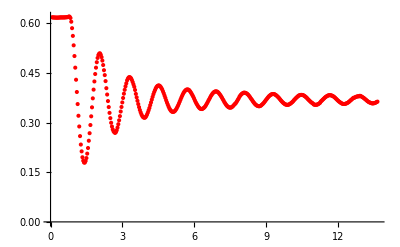

```mathematica
Experiment=ListPlot[Data2,PlotStyle->Red, PlotRange->All]
```

```mathematica
mspring = .023
```

0.023

```mathematica
mobject = 0.429
```

0.429

```mathematica
(* define constants and initial conditions *)
Manipulate[
g = 9.8;
m = 0.429;
x= 0.508;
xeq=0.366;
vx=0.0766800133467;
ti = 2.0313;
tf = 14;
dt = .03;
(* define an array where we store the results of the simulation *) 
modeldata ={{ti,x}};

(* set up the procedure for step-by-step solution of the equation of motion *)
For[t=ti,t<tf,
(* calculate the acceleration *)
Fs = -keff(x-xeq);
Ff2=-Sign[vx]*(Abs[vx])^2*c2;

ax=(Fs+Ff2)/m;
(* redefine y, vy, in terms of the values from the previous step *)

vx = vx+ ax dt;
x= x + vx dt ;
t= t + dt;

(* add the results of the calculation step to the array *)
modeldata = Append[modeldata,{t,x}];

];


(* plot the simulation and compare with the exact result *)
dataplot = ListPlot[modeldata];
Show[{dataplot,Experiment},PlotRange->All],{keff,10,13},{c2,0.8,1.5}]
```

Can look at driving frequency and frequency response of the system.  Plot Response vs driving frequency, Amplitude vs Driving frequency, Prediction of simulation vs observations,